```mathematica
ClearAll["`*"]
```

### This notebook will merely contain a list of the Pareto-optimal methods. In other words, we provide the set of methods where the LMM will have the smallest possible error for a given value of κ

#### 2-step LMMs: Note that for κ=0 the LMM is the BDF2 method, and for κ=1 we have the Trapezoidal method. This means for κ∈(0,1) we will have LMMs with an error between -1/3 and -1/12 Due to the coefficient conditions for consistency, we can narrow down the coefficients of the LMM to the following parameters: α: {3-2 β_1-4 β_2,-4+2 β_1+4 β_2,1} β: {-2+β_1+3 β_2,β_1,β_2} This means that we only have two free parameters, β_1 and β_2

```mathematica
cond2step=((β0-β1+β2) (-2+β0+β1+β2)≤0&&(2+β0-β1-3 β2) (β0+β1+β2)≤0&&((4 β0 β2>β1^2&&β0≠β2)||β0^2+β1^2+β2^2≥6 β0 β2))&&(Abs[β2 κ^2]>Abs[β0]&&Abs[β0^2-β2^2 κ^4]>Abs[β1 κ (β0-β2 κ^2)])/.{β0->-2+β1+3 β2}//Simplify;
```

```mathematica
c32step[β1_,β2_]:=1/12 Abs[(-4+β1+8 β2)/(-1+β1+2 β2)]
```

```mathematica
κlist2=Table[{k,Quiet[Minimize[{c32step[β1,β2],cond2step/. κ->k},{β1,β2}]]},{k,0,1,1/100}];
```

```mathematica
κlist2=κlist2/.κlist2[[1,2]]->{1/3,{β1->0,β2->2/3}};
```

```mathematica
κlist2=κlist2/.κlist2[[101,2]]->{1/12,{β1->1/2,β2->1/2}};
```

#### Each element in the following list has the following structure: {{κ-value, {|Error|, {β1, β2}}}, ...}

```mathematica
κlist2
```

{{0,{1/3,{β1→0,β2→2/3}}},{1/100,{9901/30603,{β1→400/30199,β2→20000/30199}}},{1/50,{817/2601,{β1→200/7599,β2→5000/7599}}},{3/100,{9709/31827,{β1→400/10197,β2→20000/30591}}},{1/25,{601/2028,{β1→25/481,β2→625/962}}},{1/20,{127/441,{β1→80/1239,β2→800/1239}}},{3/50,{2359/8427,{β1→200/2597,β2→5000/7791}}},{7/100,{9349/34347,{β1→2800/31351,β2→20000/31351}}},{2/25,{193/729,{β1→200/1971,β2→1250/1971}}},{9/100,{9181/35643,{β1→1200/10573,β2→20000/31719}}},{1/10,{91/363,{β1→40/319,β2→200/319}}},{11/100,{3007/12321,{β1→4400/32079,β2→20000/32079}}},{3/25,{559/2352,{β1→25/168,β2→625/1008}}},{13/100,{8869/38307,{β1→5200/32431,β2→20000/32431}}},{7/50,{733/3249,{β1→1400/8151,β2→5000/8151}}},{3/20,{349/1587,{β1→80/437,β2→800/1311}}},{4/25,{541/2523,{β1→400/2059,β2→1250/2059}}},{17/100,{2863/13689,{β1→6800/33111,β2→20000/33111}}},{9/50,{2131/10443,{β1→600/2773,β2→5000/8319}}},{19/100,{8461/42483,{β1→7600/33439,β2→20000/33439}}},{1/5,{7/36,{β1→5/21,β2→25/42}}},{21/100,{8341/43923,{β1→2800/11253,β2→20000/33759}}},{11/50,{2071/11163,{β1→2200/8479,β2→5000/8479}}},{23/100,{2743/15129,{β1→9200/34071,β2→20000/34071}}},{6/25,{511/2883,{β1→200/713,β2→1250/2139}}},{1/4,{13/75,{β1→16/55,β2→32/55}}},{13/50,{673/3969,{β1→2600/8631,β2→5000/8631}}},{27/100,{8029/48387,{β1→3600/11557,β2→20000/34671}}},{7/25,{499/3072,{β1→175/544,β2→625/1088}}},{29/100,{2647/16641,{β1→11600/34959,β2→20000/34959}}},{3/10,{79/507,{β1→40/117,β2→200/351}}},{31/100,{7861/51483,{β1→12400/35239,β2→20000/35239}}},{8/25,{163/1089,{β1→800/2211,β2→1250/2211}}},{33/100,{7789/53067,{β1→4400/11837,β2→20000/35511}}},{17/50,{1939/13467,{β1→3400/8911,β2→5000/8911}}},{7/20,{103/729,{β1→560/1431,β2→800/1431}}},{9/25,{481/3468,{β1→75/187,β2→625/1122}}},{37/100,{7669/56307,{β1→14800/36031,β2→20000/36031}}},{19/50,{637/4761,{β1→3800/9039,β2→5000/9039}}},{39/100,{7621/57963,{β1→5200/12093,β2→20000/36279}}},{2/5,{19/147,{β1→40/91,β2→50/91}}},{41/100,{2527/19881,{β1→16400/36519,β2→20000/36519}}},{21/50,{1891/15123,{β1→1400/3053,β2→5000/9159}}},{43/100,{7549/61347,{β1→17200/36751,β2→20000/36751}}},{11/25,{157/1296,{β1→275/576,β2→625/1152}}},{9/20,{301/2523,{β1→240/493,β2→800/1479}}},{23/50,{1879/15987,{β1→4600/9271,β2→5000/9271}}},{47/100,{2503/21609,{β1→18800/37191,β2→20000/37191}}},{12/25,{469/4107,{β1→400/777,β2→1250/2331}}},{49/100,{7501/66603,{β1→19600/37399,β2→20000/37399}}},{1/2,{1/9,{β1→8/15,β2→8/15}}},{51/100,{7501/68403,{β1→6800/12533,β2→20000/37599}}},{13/25,{469/4332,{β1→325/589,β2→625/1178}}},{53/100,{2503/23409,{β1→21200/37791,β2→20000/37791}}},{27/50,{1879/17787,{β1→1800/3157,β2→5000/9471}}},{11/20,{301/2883,{β1→880/1519,β2→800/1519}}},{14/25,{157/1521,{β1→1400/2379,β2→1250/2379}}},{57/100,{7549/73947,{β1→7600/12717,β2→20000/38151}}},{29/50,{1891/18723,{β1→5800/9559,β2→5000/9559}}},{59/100,{2527/25281,{β1→23600/38319,β2→20000/38319}}},{3/5,{19/192,{β1→5/8,β2→25/48}}},{61/100,{7621/77763,{β1→24400/38479,β2→20000/38479}}},{31/50,{637/6561,{β1→6200/9639,β2→5000/9639}}},{63/100,{7669/79707,{β1→8400/12877,β2→20000/38631}}},{16/25,{481/5043,{β1→1600/2419,β2→1250/2419}}},{13/20,{103/1089,{β1→1040/1551,β2→800/1551}}},{33/50,{1939/20667,{β1→2200/3237,β2→5000/9711}}},{67/100,{7789/83667,{β1→26800/38911,β2→20000/38911}}},{17/25,{163/1764,{β1→425/609,β2→625/1218}}},{69/100,{7861/85683,{β1→9200/13013,β2→20000/39039}}},{7/10,{79/867,{β1→280/391,β2→200/391}}},{71/100,{2647/29241,{β1→28400/39159,β2→20000/39159}}},{18/25,{499/5547,{β1→600/817,β2→1250/2451}}},{73/100,{8029/89787,{β1→29200/39271,β2→20000/39271}}},{37/50,{673/7569,{β1→7400/9831,β2→5000/9831}}},{3/4,{13/147,{β1→16/21,β2→32/63}}},{19/25,{511/5808,{β1→475/616,β2→625/1232}}},{77/100,{2743/31329,{β1→30800/39471,β2→20000/39471}}},{39/50,{2071/23763,{β1→2600/3293,β2→5000/9879}}},{79/100,{8341/96123,{β1→31600/39559,β2→20000/39559}}},{4/5,{7/81,{β1→80/99,β2→50/99}}},{81/100,{8461/98283,{β1→10800/13213,β2→20000/39639}}},{41/50,{2131/24843,{β1→8200/9919,β2→5000/9919}}},{83/100,{2863/33489,{β1→33200/39711,β2→20000/39711}}},{21/25,{541/6348,{β1→175/207,β2→625/1242}}},{17/20,{349/4107,{β1→1360/1591,β2→800/1591}}},{43/50,{733/8649,{β1→8600/9951,β2→5000/9951}}},{87/100,{8869/104907,{β1→11600/13277,β2→20000/39831}}},{22/25,{559/6627,{β1→2200/2491,β2→1250/2491}}},{89/100,{3007/35721,{β1→35600/39879,β2→20000/39879}}},{9/10,{91/1083,{β1→120/133,β2→200/399}}},{91/100,{9181/109443,{β1→36400/39919,β2→20000/39919}}},{23/25,{193/2304,{β1→575/624,β2→625/1248}}},{93/100,{9349/111747,{β1→12400/13317,β2→20000/39951}}},{47/50,{2359/28227,{β1→9400/9991,β2→5000/9991}}},{19/20,{127/1521,{β1→1520/1599,β2→800/1599}}},{24/25,{601/7203,{β1→800/833,β2→1250/2499}}},{97/100,{9709/116427,{β1→38800/39991,β2→20000/39991}}},{49/50,{817/9801,{β1→9800/9999,β2→5000/9999}}},{99/100,{9901/118803,{β1→13200/13333,β2→20000/39999}}},{1,{1/12,{β1→1/2,β2→1/2}}}}

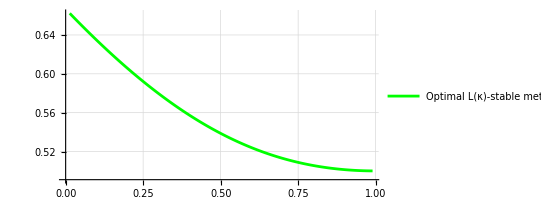

```mathematica
plt4=ListLinePlot[{β1,β2}/.κlist2[[2;;-2,2,2]],GridLines->Automatic,AspectRatio->1/2,PlotStyle->Green,PlotLegends->{"Optimal L(κ)-stable methods"}]
```

### Special 3-step LMMs (2 nonzero β - coefficients)

#### Again, thanks to the consistency conditions, the coefficients are reduced as the following: α: {-1+β2/2+(3 β3)/2,3-2 β2-4 β3,-3+(3 β2)/2+(5 β3)/2,1} β: {0,0,β2,β3}

```mathematica
σ[b_][xi_]:=Sum[b[[i+1]] xi^i,{i,0,Length[b]-1}]
```

```mathematica
c32beta[β2_,β3_]:=Module[
{a,b,sum},
a={-1+β2/2+(3 β3)/2,3-2 β2-4 β3,-3+(3 β2)/2+(5 β3)/2,1};
b={0,0,β2,β3};
sum=Abs[1/(σ[b][1])Sum[(j^3 a[[j+1]])/(3!)-(j^(3-1)b[[j+1]])/((3-1)!),{j,0,Length[a]-1}]];
sum//Simplify
]
```

```mathematica
cond2beta=((β3==1/2&&β2==1/2)||(1/2<β3<3/5&&1/2 (2-5 β3)+1/2 √(4+4 β3-15 β3^2)≤β2≤β3)||(β3==3/5&&0≤β2≤3/5)||(3/5<β3<2/3&&1/2 (2-5 β3)+1/2 √(4+4 β3-15 β3^2)≤β2≤β3)||(β3==2/3&&β2≥-2/3)||(2/3<β3<1&&-β3≤β2≤2-2 β3)||(β3==1&&-1≤β2≤0)||(1<β3<2&&-β3≤β2≤2-2 β3)||(β3==2&&β2==-2))&&Abs[β3 κ]^2>Abs[β2 β3 κ];
```

```mathematica
κlist3=Table[{k,Quiet[Minimize[{c32beta[β2,β3],cond2beta/. κ->k},{β2,β3}]]},{k,0,1,1/100}];
```

```mathematica
κlist3=κlist3/.κlist3[[1,2]]->{1/6,{β2->0,β3->3/5}};
```

```mathematica
κlist3
```

{{0,{1/6,{β2→0,β3→3/5}}},{1/100,{299/1806,{β2→602/100501,β3→60200/100501}}},{1/50,{149/906,{β2→302/25251,β3→15100/25251}}},{3/100,{33/202,{β2→1818/101509,β3→60600/101509}}},{1/25,{37/228,{β2→19/797,β3→475/797}}},{1/20,{59/366,{β2→122/4101,β3→2440/4101}}},{3/50,{49/306,{β2→918/25759,β3→15300/25759}}},{7/100,{293/1842,{β2→4298/103549,β3→61400/103549}}},{2/25,{73/462,{β2→77/1626,β3→1925/3252}}},{9/100,{97/618,{β2→5562/104581,β3→61800/104581}}},{1/10,{29/186,{β2→62/1051,β3→620/1051}}},{11/100,{289/1866,{β2→6842/105621,β3→62200/105621}}},{3/25,{2/13,{β2→234/3317,β3→1950/3317}}},{13/100,{287/1878,{β2→8138/106669,β3→62600/106669}}},{7/50,{143/942,{β2→2198/26799,β3→15700/26799}}},{3/20,{19/126,{β2→378/4309,β3→2520/4309}}},{4/25,{71/474,{β2→316/3383,β3→1975/3383}}},{17/100,{283/1902,{β2→10778/108789,β3→63400/108789}}},{9/50,{47/318,{β2→2862/27331,β3→15900/27331}}},{19/100,{281/1914,{β2→12122/109861,β3→63800/109861}}},{1/5,{7/48,{β2→8/69,β3→40/69}}},{21/100,{31/214,{β2→13482/110941,β3→64200/110941}}},{11/50,{139/966,{β2→3542/27871,β3→16100/27871}}},{23/100,{277/1938,{β2→14858/112029,β3→64600/112029}}},{6/25,{23/162,{β2→243/1759,β3→2025/3518}}},{1/4,{11/78,{β2→26/181,β3→104/181}}},{13/50,{137/978,{β2→4238/28419,β3→16300/28419}}},{27/100,{91/654,{β2→17658/114229,β3→65400/114229}}},{7/25,{17/123,{β2→574/3587,β3→2050/3587}}},{29/100,{271/1974,{β2→19082/115341,β3→65800/115341}}},{3/10,{3/22,{β2→198/1159,β3→660/1159}}},{31/100,{269/1986,{β2→20522/116461,β3→66200/116461}}},{8/25,{67/498,{β2→664/3657,β3→2075/3657}}},{33/100,{89/666,{β2→21978/117589,β3→66600/117589}}},{17/50,{133/1002,{β2→5678/29539,β3→16700/29539}}},{7/20,{53/402,{β2→938/4749,β3→2680/4749}}},{9/25,{11/84,{β2→189/932,β3→525/932}}},{37/100,{263/2022,{β2→24938/119869,β3→67400/119869}}},{19/50,{131/1014,{β2→6422/30111,β3→16900/30111}}},{39/100,{29/226,{β2→26442/121021,β3→67800/121021}}},{2/5,{13/102,{β2→17/76,β3→85/152}}},{41/100,{259/2046,{β2→27962/122181,β3→68200/122181}}},{21/50,{43/342,{β2→7182/30691,β3→17100/30691}}},{43/100,{257/2058,{β2→29498/123349,β3→68600/123349}}},{11/25,{16/129,{β2→946/3873,β3→2150/3873}}},{9/20,{17/138,{β2→1242/4981,β3→2760/4981}}},{23/50,{127/1038,{β2→7958/31279,β3→17300/31279}}},{47/100,{253/2082,{β2→32618/125709,β3→69400/125709}}},{12/25,{7/58,{β2→1044/3947,β3→2175/3947}}},{49/100,{251/2094,{β2→34202/126901,β3→69800/126901}}},{1/2,{5/42,{β2→14/51,β3→28/51}}},{51/100,{83/702,{β2→35802/128101,β3→70200/128101}}},{13/25,{31/264,{β2→572/2011,β3→1100/2011}}},{53/100,{247/2118,{β2→37418/129309,β3→70600/129309}}},{27/50,{41/354,{β2→9558/32479,β3→17700/32479}}},{11/20,{49/426,{β2→1562/5221,β3→2840/5221}}},{14/25,{61/534,{β2→623/2049,β3→2225/4098}}},{57/100,{27/238,{β2→40698/131749,β3→71400/131749}}},{29/50,{121/1074,{β2→10382/33091,β3→17900/33091}}},{59/100,{241/2154,{β2→42362/132981,β3→71800/132981}}},{3/5,{1/9,{β2→54/167,β3→90/167}}},{61/100,{239/2166,{β2→44042/134221,β3→72200/134221}}},{31/50,{119/1086,{β2→11222/33711,β3→18100/33711}}},{63/100,{79/726,{β2→45738/135469,β3→72600/135469}}},{16/25,{59/546,{β2→1456/4253,β3→2275/4253}}},{13/20,{47/438,{β2→1898/5469,β3→2920/5469}}},{33/50,{13/122,{β2→12078/34339,β3→18300/34339}}},{67/100,{233/2202,{β2→49178/137989,β3→73400/137989}}},{17/25,{29/276,{β2→391/1083,β3→575/1083}}},{69/100,{77/738,{β2→50922/139261,β3→73800/139261}}},{7/10,{23/222,{β2→518/1399,β3→740/1399}}},{71/100,{229/2226,{β2→52682/140541,β3→74200/140541}}},{18/25,{19/186,{β2→837/2206,β3→2325/4412}}},{73/100,{227/2238,{β2→54458/141829,β3→74600/141829}}},{37/50,{113/1122,{β2→13838/35619,β3→18700/35619}}},{3/4,{1/10,{β2→90/229,β3→120/229}}},{19/25,{14/141,{β2→1786/4493,β3→2350/4493}}},{77/100,{223/2262,{β2→58058/144429,β3→75400/144429}}},{39/50,{37/378,{β2→14742/36271,β3→18900/36271}}},{79/100,{221/2274,{β2→59882/145741,β3→75800/145741}}},{4/5,{11/114,{β2→76/183,β3→95/183}}},{81/100,{73/762,{β2→61722/147061,β3→76200/147061}}},{41/50,{109/1146,{β2→15662/36931,β3→19100/36931}}},{83/100,{217/2298,{β2→63578/148389,β3→76600/148389}}},{21/25,{3/32,{β2→1008/2329,β3→1200/2329}}},{17/20,{43/462,{β2→2618/5989,β3→3080/5989}}},{43/50,{107/1158,{β2→16598/37599,β3→19300/37599}}},{87/100,{71/774,{β2→67338/151069,β3→77400/151069}}},{22/25,{53/582,{β2→1067/2371,β3→2425/4742}}},{89/100,{211/2334,{β2→69242/152421,β3→77800/152421}}},{9/10,{7/78,{β2→702/1531,β3→780/1531}}},{91/100,{209/2346,{β2→71162/153781,β3→78200/153781}}},{23/25,{13/147,{β2→2254/4827,β3→2450/4827}}},{93/100,{23/262,{β2→73098/155149,β3→78600/155149}}},{47/50,{103/1182,{β2→18518/38959,β3→19700/38959}}},{19/20,{41/474,{β2→3002/6261,β3→3160/6261}}},{24/25,{17/198,{β2→2376/4913,β3→2475/4913}}},{97/100,{203/2382,{β2→77018/157909,β3→79400/157909}}},{49/50,{101/1194,{β2→19502/39651,β3→19900/39651}}},{99/100,{67/798,{β2→79002/159301,β3→79800/159301}}},{1,{1/12,{β2→1/2,β3→1/2}}}}